# Unidad 3 4 - Inducción de la señal en una guitarra eléctrica.

Una guitarra eléctrica funciona transformando la vibración de las cuerdas metálicas en una señal eléctrica que se induce en una bobina con un núcleo ferromagnético y un imán en su base. Cuando las cuerdas oscilan en el campo magnético del imán se induce una corriente en el embobinado, y los núcleos aumentan el flujo magnético a través de la pastilla. Se desea modelar cómo es que la señal proveniente de la vibración de la cuerda se transforma al ser inducida en la bobina de la guitarra eléctrica.

La implementación que aquí se muestra se basa en el desarrollo de: K. T. McDonald, Electric Guitar Pickups Joseph Henry Laboratories, Princenton University, Princenton, NJ 08544.

## Introducción a funciones relacionadas con audio

```mathematica
Play[Sin[440 2Pi t],{t,0,1}]
```

-Graphics-

```mathematica
Play[2 Sin[440  π t]+Sin[440  π t]+RandomReal[{-1,1}],{t,0,1}]
```

-Graphics-

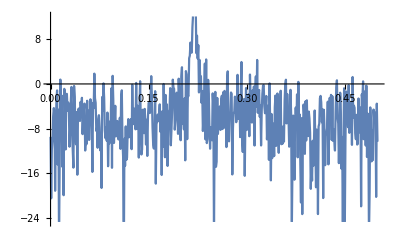

```mathematica
data=Table[2 Sin[440  π t]+Sin[440  π t]+RandomReal[{-1,1}],{t,0,1,0.001}];
Periodogram[data]
```

## Transformación de señal continua

Una primera prueba es ver cómo se transforma una señal continua generada a partir de un tono. En este caso de frecuencia 440 Hz.

```mathematica
(* Parámetros *)
SetOptions[{Plot,ListPlot,ListLinePlot},BaseStyle->FontSize->14];
imgsize = 500;
L = 0.1;
h= 0.005;
a = 0.025;
B = 0.3;
μ = 1.5;
freq = 440;

(* Señal inicial e inducida *)
y[t_] := 0.001 Sin[freq 2Pi t];
x[t_] := 0.001  Cos[freq 2Pi t];
V[t_] := B a^2 L^2 (μ-1)/(μ+1)(2x[t] x'[t](3 h^2 - L^2/4)/((h^2 + L^2/4)^3)+(2 h y'[t])/((h^2 + L^2/4)^2));

(* Gráficas y audios *)
Plot[{x[t], y[t],V[t]},{t,0,0.01}, PlotLabel->"Señal",PlotLegends->{"x(t)","y(t)", "V(t)"}]
Text["Audio de la señal"]
Play[y[t],{t,0,0.3}]
Play[V[t],{t,0,0.3}]
Text["Armónicos de la señal original en x(t)"]

(* Análisis espectral de audios *)
samplerate=10000;
data=Table[{t,x[t]},{t,0.,0.1,1/samplerate}];

time=Length[data]/samplerate;
nyq=Floor[Length[data]/2];
f = Take[10*Log10[(Abs@Fourier[data[[All,2]],FourierParameters->{1,-1}])^2],nyq];peaks = (N[(nyq-1)/time]/Length[f])FindPeaks[f];

Periodogram[data[[All,2]],SampleRate->samplerate,Frame->True,GridLines->{peaks[[All, 1]],None},FrameTicks->{{All,All},{peaks[[All, 1]],All}},GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4,ImageSize->imgsize]

Text["Armónicos de la señal original en y(t)"]

data=Table[{t,y[t]},{t,0.,0.1,1/samplerate}];

time=Length[data]/samplerate;
nyq=Floor[Length[data]/2];
f = Take[10*Log10[(Abs@Fourier[data[[All,2]],FourierParameters->{1,-1}])^2],nyq];peaks = (N[(nyq-1)/time]/Length[f])FindPeaks[f];

Periodogram[data[[All,2]],SampleRate->samplerate,Frame->True,GridLines->{peaks[[All, 1]],None},FrameTicks->{{All,All},{peaks[[All, 1]],All}},GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4,ImageSize->imgsize]

Text["Armónicos de la señal inducida"]

data=Table[{t,V[t]},{t,0.,0.1,1/samplerate}];

time=Length[data]/samplerate;
nyq=Floor[Length[data]/2];
f = Take[10*Log10[(Abs@Fourier[data[[All,2]],FourierParameters->{1,-1}])^2],nyq];peaks = (N[(nyq-1)/time]/Length[f])FindPeaks[f];

Periodogram[data[[All,2]],SampleRate->samplerate,Frame->True,GridLines->{peaks[[All, 1]],None},FrameTicks->{{All,All},{peaks[[All, 1]],All}},GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4,ImageSize->imgsize]
```

## Transformación de señal discreta (sampleo)

No siempre se tiene la ventaja de tener una señal continua, una manera más general de realizar este procedimiento es utilizando una señal basada en un número finito de muestras. Aquí se muestra el mismo procedimiento pero tomando 10000 muestras por segundo de la señal original.

```mathematica
(* Parámetros *)
SetOptions[{Plot,ListPlot,ListLinePlot},BaseStyle->FontSize->14];
L = 0.1;
h= 0.005;
a = 0.025;
B = 0.3;
μ = 1.5;
freq = 440;
samplerate = 10000;

(* Transformación *)
xt = Table[{t,0.001 Sin[freq 2 π t]},{t,0,0.3,1/samplerate}];
yt = Table[{t,0.001 Cos[freq 2 π t]},{t,0,0.3,1/samplerate}];
x = Interpolation[xt];
y = Interpolation[yt];
V[t_] := B a^2 L^2 (μ-1)/(μ+1)(2x[t] x'[t](3 h^2 - L^2/4)/((h^2 + L^2/4)^3)+(2 h y'[t])/((h^2 + L^2/4)^2));

(* Gráfica y audios *)
Plot[{x[t], y[t],V[t]},{t,0,0.01}, PlotLabel->"Señal"]
Text["Audio de la señal"]
Play[y[t],{t,0,0.3}]
Play[V[t],{t,0,0.3}]
```

## Transformación de audio en archivo

La ventaja de transformar una señal por muestras es que nos permite trabajar archivos de audio, que por lo general poseen una tasa de muestreo de 44000 muestras por segundo.

```mathematica
(* Parámetros e importa archivo *)
SetDirectory[NotebookDirectory[]];
audio = Import["5th_String_A.aiff"];
SetOptions[{Plot,ListPlot,ListLinePlot},BaseStyle->FontSize->14];
L = 0.1;
h= 0.005;
a = 0.025;
B = 0.3;
μ = 1.5;
samplerate = audio[[1,2]];
time = Table[N[i/audio[[1,2]]], {i,0,Length[audio[[1,1,1]]]-1}];
playtime = Length[audio[[1,1,1]]]/audio[[1,2]];

(* Transformación *)
xt = Transpose[{time, audio[[1,1,1]] }];
yt =  Transpose[{time, audio[[1,1,1]] }];
x = Interpolation[xt];
y = Interpolation[yt];
V[t_] := B a^2 L^2 (μ-1)/(μ+1)(2x[t] x'[t](3 h^2 - L^2/4)/((h^2 + L^2/4)^3)+(2 h y'[t])/((h^2 + L^2/4)^2));

(* Audios *)
Text["Audio de la señal"]
inex = Play[y[t],{t,0,playtime},SampleRate->44100]
outex = Play[V[t],{t,0,playtime},SampleRate->44100]
```